```mathematica
(*Basic Calculations and Manipulations*)(*Define variables*)a=2;
b=3;
c=1;

(*Perform arithmetic operations*)
sum=a+b;
difference=a-b;
product=a*b;
quotient=a/b;

(*Display results*)
Print["Sum: ",sum];
Print["Difference: ",difference];
Print["Product: ",product];
Print["Quotient: ",quotient];

(*Solve a simple equation*)
equation=a x^2+b x+c==0;
solution=Solve[equation,x];

(*Display the solution*)
Print["Quadratic Equation Solution: ",solution];

(*Perform symbolic manipulation*)
expression=(a+b)^2;
expandedExpression=Expand[expression];

(*Display the expanded expression*)
Print["Expanded Expression: ",expandedExpression];
```

Sum: 5

Difference: -1

Product: 6

Quotient: 2/3

Quadratic Equation Solution: {{x→-1},{x→-1/2}}

Expanded Expression: 25

{{x→-1},{x→-1/2}}

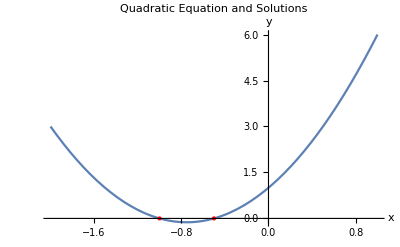

```mathematica
(*Plotting the Quadratic Equation and Solutions*)(*Define the quadratic equation coefficients*)a=2;
b=3;
c=1;

(*Define the quadratic equation*)
quadraticEquation[x_]:=a x^2+b x+c

(*Solve the quadratic equation*)
solution=Solve[quadraticEquation[x]==0,x]

(*Plot the quadratic equation and its solutions*)
Plot[quadraticEquation[x],{x,-2,1},Epilog->{Red,Point[{x,0}/. solution]},PlotLabel->"Quadratic Equation and Solutions",AxesLabel->{"x","y"}]
```